```mathematica
num=64;
points=Table[Table[0,{j,1,num}],{i,1,num}];
points1=Table[0,{i,1,num}];
root=π/2;
For[i=1,i<num+1,i++,
Clear[y];
u0=N[(0.6664i)/num];
sol=NDSolve[{y''[x]+y[x]-3/2 y[x]^2==0,y[0]==u0,y'[0]==0},y,{x,0,14}];
t=y/.sol[[1,1]];
root=x/.FindRoot[t[x],{x,root}][[1]];
points1[[i]]=root;
points[[i,1]]=root;
root1=root;
For[j=1,j<num-1,j++,
root1=x/.FindRoot[t[x]-(u0 j)/num,{x,root 1}][[1]];
points[[i,j+1]]=root1;
If[root1>root,Print["gg"]]
];
points[[i,num]]=0;
]
```

InterpolatingFunction::dmval: Input value {29.7371} lies outside the range of data in the interpolating function. Extrapolation will be used.

```mathematica
Export["E:\\files\\C++\\BlackHole\\BlackHoleRendering\\BlackHoleRendering\\BlackHoleRendering\\resources\\case2.txt",points,"Table"];
Export["E:\\files\\C++\\BlackHole\\BlackHoleRendering\\BlackHoleRendering\\BlackHoleRendering\\resources\\case2_edge.txt",points1,"Table"]
```

E:\files\C++\BlackHole\BlackHoleRendering\BlackHoleRendering\BlackHoleRendering\resources\case2_edge.txt

```mathematica
ut=Interpolation[points];(*x^2 Log[(3/2-1/(x-2/3))]*)
Plot[ut[x], {x,0 ,0.6661691542288557}]
```

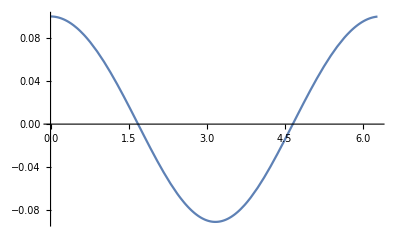

```mathematica
Clear[y];
t=y/.NDSolve[{y''[x]+y[x]-3/2 y[x]^2==0,y[0]==0.1,y'[0]==0},y,{x,0,14}][[1,1]];
Plot[t[x],{x,0,2π}]
```

```mathematica
FindRoot[t[x]-0.05,{x,1}]
```

{x→1.12786}

```mathematica
(1+2Sin[ArcSin[6.75*(1-0.1)/(10*10)-1]/3])/3
```

0.0695438

```mathematica
1/0.06954377874023288
```

14.3794

```mathematica
points1
```

{1.58131,1.59205,1.60302,1.61421,1.62566,1.63735,1.6493,1.66153,1.67404,1.68684,1.69995,1.71338,1.72714,1.74124,1.75571,1.77055,1.78579,1.80144,1.81752,1.83405,1.85106,1.86857,1.88661,1.90519,1.92436,1.94414,1.96458,1.9857,2.00754,2.03016,2.0536,2.07792,2.10316,2.12941,2.15672,2.18517,2.21486,2.24587,2.27832,2.31233,2.34803,2.38558,2.42516,2.46696,2.51123,2.55824,2.60829,2.66178,2.71915,2.78094,2.84781,2.92059,3.00031,3.0883,3.18631,3.29671,3.42279,3.56942,3.74406,3.95922,4.23823,4.63313,5.30767,8.99202}